### Discontinuous Galerkin Method for Rank 3

```mathematica
switch[x_]:=If[x>0,x,0];
```

```mathematica
legendre[n_,x_]:=LegendreP[n-1,2 x-1] √(2 (n-1)+1)
```

```mathematica
f11[x_]:=If[Abs[x]>1,0,If[x≥0,1/(√2),-1/(√2)]]
f21[x_]:=If[Abs[x]>1,0,If[x≥0,√(3/2) (-1+2 x),f21[-x]]]
f22[x_]:=If[Abs[x]>1,0,If[x≥0,√(1/2) (-2+3 x),-f22[-x]]]
f31[x_]:=If[Abs[x]>1,0,If[x≥0,1/3 √(1/2) (1-24 x+30 x^2),-f31[-x]]]
f32[x_]:=If[Abs[x]>1,0,If[x≥0,1/2 √(3/2) (3-16 x+15 x^2),f32[-x]]]
f33[x_]:=If[Abs[x]>1,0,If[x≥0,1/3 √(5/2) (4-15 x+12 x^2),-f33[-x]]]
```

```mathematica
f2[fnumber_]:=Which[fnumber==1,f21,fnumber==2,f22]
f3[fnumber_]:=Which[fnumber==1,f31,fnumber==2,f32,fnumber==3,f33]
```

```mathematica
v3[fnumber_,level_,place_]:=If[level==0,legendre[fnumber,#1]&,2^(level/2) f3[fnumber][2^level #1-(2 place-1)]&]
```

```mathematica
innerProduct[f_,g_,level_,place_]:=NIntegrate[f[x] g[x],{x,(place-1) 2^(-switch[level-1]),place 2^(-switch[level-1])}]
```

```mathematica
iterate3[n_]:=Module[{fnumber,level,place,hashMap,count},hashMap=Table[0,{i,1,3 2^n}];count=1;For[level=0,level≤n,level++,For[place=1,place≤2^switch[level-1],place++,For[fnumber=1,fnumber≤3,fnumber++,hashMap⟦count++⟧={fnumber,level+1,place}]]];Return[hashMap];]

getCoefficients3[f_,fnumber_,level_,place_]:=innerProduct[f,v3[fnumber,level,place],level,place]
```

```mathematica
fullCoefficients3[f_,n_]:=Module[{iters,i,hash,count,coeff},
iters=iterate3[n];
hash=Table[0,{i,1,Length[iters]}];
For[i=1,i≤Length[iters],i++,
coeff=getCoefficients3[f,iters⟦i⟧⟦1⟧,iters⟦i⟧⟦2⟧-1,iters⟦i⟧⟦3⟧];hash⟦i⟧=iters⟦i⟧->coeff;];Return[SparseArray[hash]]]

reconstruct3[coeffs_,x_,n_]:=Module[{fnumber,level,place,value},
value=0;
For[level=0,level≤n,level++,
For[place=1,place≤2^switch[level-1],place++,
For[fnumber=1,fnumber≤3,fnumber++,
value+=coeffs⟦fnumber,level+1,place⟧ v3[fnumber,level,place][x];
]]];Return[value]]
```

### Discontinuous Galerkin Method Calculation

```mathematica
coeffs=fullCoefficients3[Sin[Pi #]&,4]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999615071571260003527542668116945279166429827455431222915649414}. NIntegrate obtained 1.21973×10^-17 and 1.38379×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999615071571260003527542668116945279166429827455431222915649414}. NIntegrate obtained -1.82146×10^-17 and 2.20594×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999615071571260003527542668116945279166429827455431222915649414}. NIntegrate obtained -4.06034×10^-17 and 1.18728×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

SparseArray[<48>, {3, 5, 8}]

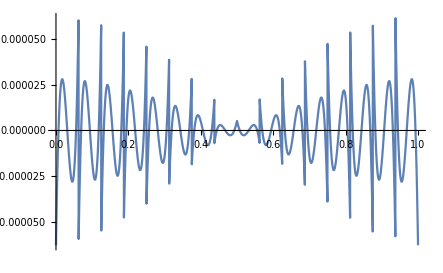

```mathematica
Plot[reconstruct3[coeffs,x,4]-Sin[Pi x],{x,0,1}]
```

```mathematica
dg3Error=Table[Sqrt[.0062 Sum[(reconstruct3[#,x,n]-Sin[Pi x])^2,{x,0,1,.0062}]&@fullCoefficients3[Sin[Pi #]&,n]],{n,1,5}]//Quiet
```

{0.00853766,0.00112029,0.00014118,0.0000179772,2.38176×10^-6}

### Error Comparision

```mathematica
hatError={0.1508769697455965,0.03928438418484165,0.00992096007189525,0.0024865565781406348,0.0006221332775942362,0.000155528179664707,0.000038883874328406936,9.721040536122335*^-6};
```

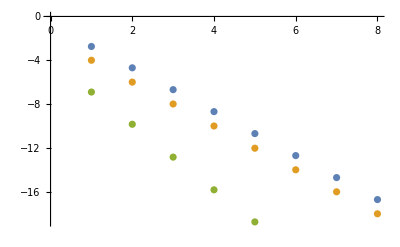

```mathematica
ListPlot[{hatError,dg2Error,dg3Error}//Log2]
```